2.48133×10^76

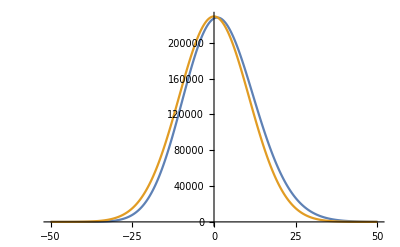

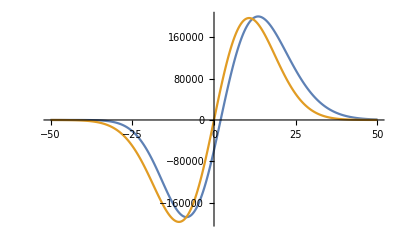

```mathematica
Get["MaTeX`"]
NA:=6.02214*10^23
m1:=1.008/NA/1000
m2:=35.45/NA/1000
m:=(m1 m2)/(m1+m2)
hbar:=1.054571726*10^-34
h:=2Pi hbar
c:=299792458
w:=2Pi c *2989*100
De:=h*c* 4.325*10^6
a:=((w^2 m)/(4Pi hbar c 4.325*10^6))^(1/2)
lambda:=Sqrt[2m De]/(a hbar)
Gamma[2lambda]
z[x_]:=2lambda Exp[-a x]
t[x_]:=x/10^12
psi00[x_]:=1/4 Log[(m w)/(Pi hbar)]-(m w t[x]^2)/(2hbar)
psi10[x_]:=1/4 Log[(m w)/(Pi hbar)]+Log[1/Sqrt[2]]+Log[2Sqrt[(m w)/hbar]*t[x]]-(m w t[x]^2)/(2hbar)
psi01[x_]:=1/2 Log[((2 lambda-1) a)/Gamma[2 lambda]] +(lambda-1/2)(Log[2lambda]-a t[x])-1/2 z[t[x]]
psi11[x_]:=1/2 Log[((2 lambda-3) a)/Gamma[2 lambda-1]] +(lambda-3/2)(Log[2lambda]-a t[x])-1/2 z[t[x]]

Plot[{Exp[psi01[x]],Exp[psi00[x]]},{x,-50,50},
PlotPoints->2000,MaxRecursion->6,WorkingPrecision->30,
PlotLegends->{MaTeX["\psi_0"],MaTeX["\psi_0'"]},
AxesLabel->{MaTeX["x/\\text{pm}"],MaTeX["\psi(x)"]},
LabelStyle->Directive[FontFamily->"CMU Serif",FontSize->10.5]
]
Plot[{Exp[psi11[x]](2lambda-2-z[t[x]]),Exp[psi10[x]]},{x,-50,50},
PlotPoints->2000,MaxRecursion->6,WorkingPrecision->30,
PlotLegends->{MaTeX["\psi_1"],MaTeX["\psi_1'"]},
AxesLabel->{MaTeX["x/\\text{pm}"],MaTeX["\psi(x)"]},
LabelStyle->Directive[FontFamily->"CMU Serif",FontSize->10.5]
]
```